```mathematica
rt=D[{x[t], y[t]Cos[θ],y[t]Sin[θ]},t]
rθ=D[{x[t], y[t]Cos[θ],y[t]Sin[θ]},θ]
```

{x'[t],Cos[θ] y'[t],Sin[θ] y'[t]}

{0,-Sin[θ] y[t],Cos[θ] y[t]}

```mathematica
nV = Cross[rt,rθ]
(D[nV/Sqrt[nV.nV],{{t,θ}}])//FullSimplify//MatrixForm
```

{Cos[θ]^2 y[t] y'[t]+Sin[θ]^2 y[t] y'[t],-Cos[θ] y[t] x'[t],-Sin[θ] y[t] x'[t]}

((y[t]^3 x'[t] (-y'[t] x''[t]+x'[t] y''[t]))/((y[t]^2 (x'[t]^2+y'[t]^2))^(3/2)) | 0
(Cos[θ] y[t]^3 y'[t] (-y'[t] x''[t]+x'[t] y''[t]))/((y[t]^2 (x'[t]^2+y'[t]^2))^(3/2)) | (Sin[θ] y[t] x'[t])/(√(y[t]^2 (x'[t]^2+y'[t]^2)))
(Sin[θ] y[t]^3 y'[t] (-y'[t] x''[t]+x'[t] y''[t]))/((y[t]^2 (x'[t]^2+y'[t]^2))^(3/2)) | -(Cos[θ] y[t] x'[t])/(√(y[t]^2 (x'[t]^2+y'[t]^2))))

```mathematica
Module[{x,y},
x=Function[t,t];
y=Function[t,((t+10)/10)^2];
ParametricPlot3D[{x[t], y[t]Cos[θ],y[t]Sin[θ]},{t,0,10},{θ,0,2π}]
]
```

-Graphics3D-

```mathematica
FullSimplify[(y[t]^3 (-y'[t] x''[t]+x'[t] y''[t]))/((y[t]^2 (x'[t]^2+y'[t]^2))^(3/2))*(- x'[t])/(y[t] √(x'[t]^2+y'[t]^2))]
```

-(Cosh[t] √(Sech[t]^2 Tanh[t]^2))/(√(Tanh[t]^2))

```mathematica
Module[{},
(*x[t_]:=t-Tanh[t];
y[t_]:=Sech[t];*)
x[t_]:=ArcSech[t]-√(1-t^2);
y[t_]:=t;
(-y'[t] x''[t]+x'[t] y''[t])/((x'[t]^2+y'[t]^2)^(3/2))*-x'[t]/(y[t] √(x'[t]^2+y'[t]^2))
]//FullSimplify[#,Assumptions->t>0]&
```

-1

```mathematica
(f[x]^3 f''[x])/((f[x]^2 (1+f'[x]^2))^(3/2))*==-1
```

```mathematica
NDSolve[{(-y'[t] x''[t]+x'[t] y''[t])/((x'[t]^2+y'[t]^2)^2)*- x'[t]==-1,x'[t]^2+y'[t]^2==1,x[t]==0,y[0]==1,x'[0]==0,y'[0]==-1},{x[t],y[t]},t]
```

NDSolve::overdet: There are fewer dependent variables, {x[t],y[t]}, than equations, so the system is overdetermined.

NDSolve[{-(x'[t] (-y'[t] x''[t]+x'[t] y''[t]))/((x'[t]^2+y'[t]^2)^2)==-1,x'[t]^2+y'[t]^2==1,x[t]==0,y[0]==1,x'[0]==0,y'[0]==-1},{x[t],y[t]},t]

```mathematica
Plot[InterpolatingFunction[…][t],{t,1,2}]
```

-Graphics-

```mathematica
{t-Tanh[t],Sech[t]}/.t->1.9611797513715394
D[{t-Tanh[t],Sech[t]},t]/.t->1.9611797513715394
```

{1.,0.275923}

```mathematica
{0.9238665144466545,-0.26521157201533285}
-0.26521157201533285/0.9238665144466545
```

{0.923867,-0.265212}

-0.287067

```mathematica
NSolve[s-Tanh[s],s]
```

{{s→0.0310763},{s→-0.0155322+0.0269094 ⅈ},{s→-0.0155322-0.0269094 ⅈ}}

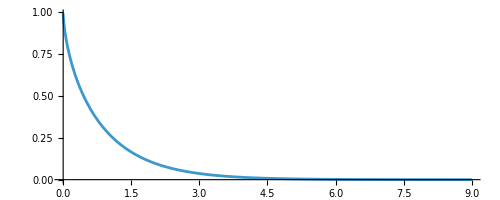

```mathematica
ParametricPlot[{t-Tanh[t],Sech[t]},{t,0.1,10}]
```

```mathematica
ArcSech[t]-Tanh[ArcSech[t]]
```

-√((1-t)/(1+t)) (1+t)+ArcSech[t]

```mathematica
D[{u, u v, u + v},u]
D[{u, u v, u + v},v]
ParametricPlot3D[
{u, u v, u + v}, {u, -20, 20}, {v,-20 ,20}
]
```

{1,v,1}

{0,u,1}

-Graphics3D-